{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3}

{1.×10^-7,4.×10^-7,9.×10^-7,1.6×10^-6,2.5×10^-6,3.6×10^-6,4.9×10^-6,6.4×10^-6,8.1×10^-6,0.00001,0.0000121,0.0000144,0.0000169,0.0000196,0.0000225,0.0000256,0.0000289,0.0000324,0.0000361,0.00004,0.0000441,0.0000484,0.0000529,0.0000576,0.0000625,0.0000676,0.0000729,0.0000784,0.0000841,0.00009}

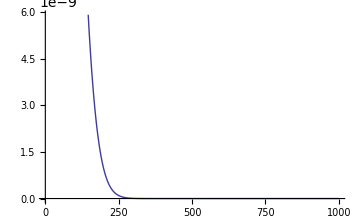

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ℏ=1.;
M=1000;
k0=0.01;
imax=30;
K=Table[K=k0*index,{index,1,imax}]
l=0;
U0=(ℏ^2 k0^2)/(2M);
Energ=Table[2*(ℏ^2 K[[index]]^2)/(2M),{index,1,imax}]
(*U0=0.;*)
σ=100.;
ϵ=0.1;
XM=10000ϵ;
U[r_]=U0*ⅇ^(-r^2/σ^2);
Plot[U[r],{r,ϵ,XM}]
TT=Table[0,{index,1,imax}]
```

{0.0430672,0.0666369,0.0636842,0.0456087,0.030383,0.0249016,0.0240939,0.0219168,0.0180464,0.0153546,0.0146718,0.0142372,0.0128423,0.011269,0.0105641,0.0104149,0.00990761,0.00898486,0.00832538,0.00815868,0.00799457,0.0074912,0.00694149,0.00670825,0.0066482,0.00640812,0.0060007,0.00572772,0.0056649,0.00557094}

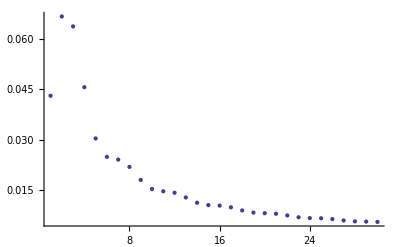

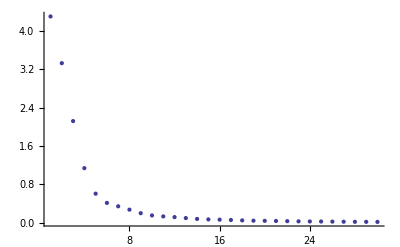

```mathematica
Do[
E1=χ''[r]+(2 M/ℏ^2(Energ[[index]]-U[r])-(l(l+1))/r^2)χ[r]==0;
E2=χ[ϵ]==ϵ^(l+1)/((2l+1)!!);
E3=χ'[ϵ]==((l+1)ϵ^l)/((2l+1)!!);
s=NDSolve[{E1,E2,E3},χ,{r,ϵ,XM}];
H[r_]=χ[r]/.s[[1]];
Ha[r_]=rSphericalBesselJ[l,√((2M*Energ[[index]])/ℏ^2)r];
(* Plot[{H[r],Ha[r]},{r,ϵ,XM},PlotStyle->{Blue,Red}] *)
sl[r_]=r*SphericalBesselJ[l,√((2M*Energ[[index]])/ℏ^2)r];
cl[r_]=r*SphericalBesselY[l,√((2M*Energ[[index]])/ℏ^2)r];
T[r0_]=-(H[r0]sl'[r0]-H'[r0]sl[r0])/(H[r0]cl'[r0]-H'[r0]cl[r0]);
(* Plot[T[r0],{r0,1ϵ,1000ϵ}] *)
TT[[index]]=T[50];,{index,1,imax}]
TT
ListPlot[TT]
A=Table[0,{index,1,imax}];
Do[A[[index]]=TT[[index]]/K[[index]],{index,1,imax}]
ListPlot[A]
```